# Project-32. Task: Train

## Mikhail Rudakov, BS19-02, Innopolis University

## Goals of the project

1) Solve physics problem analytically with the use of Wolfram Mathematica.
2) Learn basics of the Wolfram Mathematica language that are useful for solving scientific tasks.
3) Visualise the problem and let user vary parameters to see how system behaves.

## Problem statement

Train with length of 300 m is moving with constant speed v_train = 72 km/h in the direction of an unregulated crossing. Perpendicularly to the railway, car is driving on the highway with constant speed v_car. When head of the train was 600m away from crossing, car was 700m before the crossing.
a) What values of v_car are safe, i.e. train and car do not collide anytime?
b) Given v_car = 36 km/h, what is the minimum distance between nearest point of the train and the car during motion? Round the answer to the nearest integer.

## Solution

In the solution, we treat train as a line segment on the plane, and car as a point on the plane.  Train is moving along y-axis down to the origin, and car is moving along x-axis from right to the left, to the origin. Hence, railway crossing is the origin of the coordinate system.

### (a) Safe speed

```mathematica
(* Initialize variables from the problem statement. They could be changed anyhow wanted *)
trainLength = 300 ;(* length of the train *) 
trainVelocity = 72 * 1000 / 3600 ;(* velocity of the train in m/s - we convert immediately to simplify solution's expressions *)
trainDistance = 600; (* distance from the head of the train to the crossing *)
carDistance = 700 ;(* distance from the car to the crossing. *)
Clear[carVelocity]; (* velocity of the car *) (* Clear[] is used to make sure this variable is empty, not a number from any other part of the sultion *)
Clear[time]; (* time passed from initial position *)

(* x = x0 + Subscript[v, x] * t *)
carPosition={carDistance - time* carVelocity,0}; 
(* Position of the car - point on XY-plane. X-coordinate is variable as it depends on time - as car moves to the crossing *)
trainPosition=Line[{{0, trainDistance - time * trainVelocity}, {0, trainDistance + trainLength - time* trainVelocity}}];
(* Position of the train - Line Segment on XY-plane. Y-coordinate equals initial distance (for head and tail) minus distance train already covered *)
```

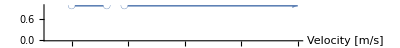

```mathematica
(* Solve inequality for carVelocity such that objects do not collide and plot graph *)
(* Syntax: NumberLinePlot[{inequality to plot},{variable, left boundary value, right boudnary value} {{attributes of plotting -> value}} *)
NumberLinePlot[
(* Solve inequality with respect to some variable on some domain *)
(* Reduce[{inequality}, {variable}, {domain}}] *)
Reduce[
(* RegionNearest[line, point] - point where distance from line to the point is minimized. Not neccessarily line and point - *)(* any 2 polygons. Point on the first polygon which is closest to the second polygon is returned *)
ForAll[time, RegionNearest[trainPosition,carPosition] !=carPosition]   (* For any moment in time, the car and the train do not collide. Hence,    nearest point between line and point should not be the point itself at any moment of time. 
ForAll[variable, expression] - states that expression should be true for any value of variable *)
&& carVelocity>0, (* Velocity of the car should be positive *)
carVelocity, (* solve inequality with respect to this variable *)
Reals (* domain for solutions of inequality *)
],

 {carVelocity,-10,100}, (* Variable to plot inequality, ranges for variable to plot on the graph *)

PlotTheme -> "Detailed", (* Detailed display of solution, with exact range *)
AxesLabel->{HoldForm["Velocity [m/s]"],None}, (* Axis label *)
PlotLabel->HoldForm["Safe velocities for the car"], (* Plot lable *)
LabelStyle->{FontFamily->"Alegreya SC", GrayLevel[0],Italic} (* Label style & font *)
]
```

### (b) Minimum distance

```mathematica
Clear[time] (* Clear variable *)
carVelocity = 36 * 1000 / 3600; (* Exact velocity from the conditions *)
carPosition={carDistance - time* carVelocity,0};
trainPosition=Line[{{0, trainDistance - time * trainVelocity}, {0, trainDistance + trainLength - time* trainVelocity}}];
(* Positions of car and train are calculated the same way as in (a) *)
Round[Minimize[RegionDistance[trainPosition,carPosition],time][[1]]]
(* RegionNearest[] computes the point on the line that is closest to the point. EulcildeanDistance[] computes the distance between two points on the plane (just distance between points in n-dimension space, in general). In our case, we find the distance between car and closest point to the car on the train - this is indeed distance between them. Then, we use Minimize[expression, variable] to find minimum value of the expression with respect to variable. Function returns minimum value of the expression and variable value when it is reached *)
```

224

## Answer

(a) Safe velocities for the car (in [km/h]): 0 < v_car< 56∪ v_car> 84.
(b) Minimal distance between the car and the train, when v_car= 36 km/h, is: d_min ≂ 224 m, achieved in time = 50 s from the initial moment.

## Visualisation

```mathematica
(* Manipulate some parameteres - Manipulate[figure, variables for manipulating]*)
Manipulate[
(* Column of some entities - Graphics and Text entry in this case *)
Column[{Graphics[ (* Graphics - picture on the coordinate plane (not neccessary, has wide functionality *)
{
{PointSize[0.03],Blue, Point[{carDistance - time * carVelocity,0}]}, (* Point on the graph. [Size, Color, Point(itself)]. Order of parameters may vary*){Brown,Thickness[0.02],Line[{{0, trainDistance - time * trainVelocity}, {0, trainDistance + trainLength - time * trainVelocity}}]},
(* Line on the graph. *)
{Red, Dashed, Thickness[0.01],Line[{{carDistance - time * carVelocity,0}, RegionNearest[Line[{{0, trainDistance - time * trainVelocity}, {0, trainDistance + trainLength - time * trainVelocity}}],{carDistance - time * carVelocity,0}]}]}
},
(* Setting of layout. Showing axis, fixed size of the image, set range of plotting *)
 Axes->True, ImageSize->{500,500}, PlotRange -> {{-carDistance * 1.1, carDistance * 1.1}, {-(trainDistance + trainLength) * 1.1, (trainDistance + trainLength) * 1.1}}
], 
(* Text frame for distance. Labeled[.., labelText] *)Labeled[Framed[Round[RegionDistance[Line[{{0, trainDistance - time * trainVelocity}, {0, trainDistance + trainLength - time * trainVelocity}}],{carDistance - time * carVelocity,0}],2]],"Distance between car and train, rounded [m]"]}],
(* Variables for manipulating as a list. Syntax: {{variable, default value, label}, left boundary, right boundary}*)
{{carVelocity, 10, "Car Velocity [m/s]"},0, 100}, {{time,0, "Time [s]"}, 0, 400}, {{trainLength,300, "Length of train [m]"}}, 
 {{trainDistance,600, "Distance from train to junction [m]"}},{{trainVelocity,20, "Train velocity [m/s]"}},
{{carDistance,700, "Distance from car to junction [m]"}}
]
(* Graphical representation of the model - you interact with the model *)
```

## Additional comments on Wolfram Mathematica

1) Semicolons may be used to suppress output of the lines that are just variable assignment
2) Expressions like \[Expression] may be used inline to represent special symbols. Also key shortcuts like ctrl + ‘-‘ exists_(subtext in this case)
3) Don’t forget to clear your variables not to get confused! Even if you deleted some code with variable, but executed it, it is still in the system.
4) Internal Wolfram Mathematica Documentation is a perfect tutorial. There are often some beautiful and useful examples how one may use some functionality.
5) Some fragments of code are repeated in Visualization part. This is not good design, repeated parts should be separate variables / functions, but it is hard to implement this as manipulate parameters are local variables. One should use Dynamic and some nice layout similar to Manipulate’s one to solve this issue.
6) Conversion between km/h and m/s may be a function applied automatically when needed, not hard-coded.
7) Graph may be displayed not very well for strange input. May be fixed, probably, with some additional work on ranges and image size.

Overall, my experience with Wolfram Mathematica is great. It is a powerful tool to solve tasks arising not only in olympiads, as I solved, but some everyday life simulations or computational tasks as well. Although I am not a scientist using Mathematica for research purposes, I am sure it is a great tool to model and compute anything one can imagine. Of course, one should be experienced enough to use functionality of Mathematica in the most efficient way, and I am not that person. However, I quite recommend trying Mathematica for students and researchers who are working with computational tasks and maybe want to model solutions for presentations. Mathematica is great for these goals. I hope I would have some more experience with Mathematica in the future.